```mathematica
codbar=Import["Google Drive/jie_programs/QHlattice/data_laughberryphase/berry_laughlin_may18","Table"];
n:=Length[codbar];
(*n=n-12;*)
codbar[[n]];
grid=20;
xaxis=Table[0.5/grid*i,{i,1,n,1}];
(*λ1=Table[codbar[[i]][[5]],{i,1,n,1}] + ⅈ*Table[codbar[[i]][[6]],{i,1,n,1}] ;
λ2=Table[codbar[[i]][[7]],{i,1,n,1}] + ⅈ*Table[codbar[[i]][[8]],{i,1,n,1}] ;
λ3=Table[codbar[[i]][[9]],{i,1,n,1}] + ⅈ*Table[codbar[[i]][[10]],{i,1,n,1}] ;*)
amp1=Table[{xaxis[[i]],codbar[[i]][[5]]},{i,1,n,1}];
amp2=Table[{xaxis[[i]],codbar[[i]][[7]]},{i,1,n,1}];
amp3=Table[{xaxis[[i]],codbar[[i]][[9]]},{i,1,n,1}];
ang1=Table[{xaxis[[i]],codbar[[i]][[6]]/(2π)},{i,1,n,1}];
ang2=Table[{xaxis[[i]],codbar[[i]][[8]]/(2π)},{i,1,n,1}];
ang3=Table[{xaxis[[i]],codbar[[i]][[10]]/(2π)},{i,1,n,1}];
```

```mathematica
phase1=Table[ang1[[i]][[2]],{i,1,n,1}];
phase2=Table[ang2[[i]][[2]],{i,1,n,1}];
phase3=Table[ang3[[i]][[2]],{i,1,n,1}];
phase:=phase1+phase2+phase3
Sum[phase[[i]],{i,1,n}]
```

4.31685

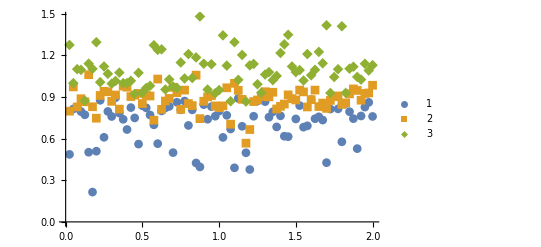

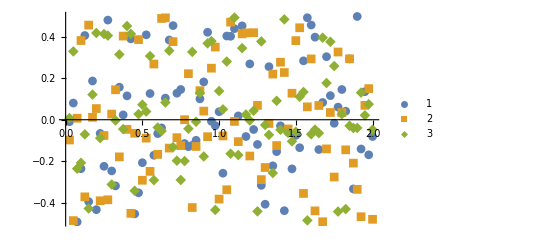

```mathematica
ListPlot[{amp1,amp2,amp3},PlotLegends->{"1","2","3"},PlotMarkers->Automatic]
ListPlot[{ang1,ang2,ang3},PlotLegends->{"1","2","3"},PlotMarkers->Automatic]
```

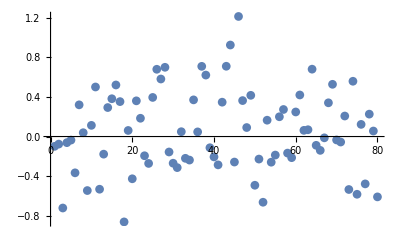

```mathematica
ListPlot[phase,PlotMarkers->Automatic]
```